# Setup

### goodlabel

```mathematica
goodlabel::usage="Evaluate[goodlabel[xlabel,ylabel, xstyle, ystyle]] makes plot labels with the desired style. Labels should be passed as strings.";
goodlabel[x_,y_]:={Frame->{{True,False},{True,False}},FrameLabel->{x,y}};
goodlabel[x_,y_,style_]:=goodlabel[x,y,style,style];goodlabel[x_,y_,xstyle_, ystyle_]:={Frame->{{True,False},{True,False}},FrameLabel->{Style[x,xstyle],Style[y,ystyle]}};
```

## sims

```mathematica
sims = SemanticImport[FileNameJoin[{NotebookDirectory[],"MH_data.txt"}]];
```

```mathematica
sims=sims[All,<|#,"dhomLow"->#hom-#homLow,"dhomHigh"->#homHigh-#hom|>&];
```

```mathematica
αlist = sims[All,#alpha&]//DeleteDuplicates//Normal//Sort;coallist = sims[All,#coal&]//DeleteDuplicates//Normal//Sort;
μlist = sims[All,#mu&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
clist = sims[All,#c&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
cdfsims = SemanticImport[FileNameJoin[{NotebookDirectory[],"CDF_data.txt"}]];
```

```mathematica
cdfsims=cdfsims [All,<|#,"dcdfLow"->#cdf-#cdfLow,"dcdfHigh"->#cdfHigh-#cdf|>&];
```

## functions

```mathematica
fLT[x_,μ_, α_, Dα_]:=NIntegrate[(Cos[k x]/π)/(μ+ Dα k^α),{k,0,∞}];
fLT[x_,μ_, α_]:=fLT[x,μ,α,250^α/2];
```

```mathematica
coeff[c_,μ_,α_,Dα_]:=1/(2/c+(μ/Dα)^(1/α)/(α Sin[π/α]μ));
coeff[c_,μ_,α_]:=coeff[c,μ,α,250^α/2];
```

```mathematica
xscale[μ_,α_,Dα_]:=(Dα/μ)^(1/α);
xscale[μ_,α_]:=xscale[μ,α,250^α/2];
```

```mathematica
homscale[coal_,μ_,α_,Dα_]:=(1/π)/(Csc[π/α]/α+ 2 (Dα/μ)^(1/α)μ/coal);
homscale[coal_,μ_,α_]:=homscale[coal,μ,α,250^α/2];
```

```mathematica
approxhomscale[coal_,μ_,α_,Dα_]:=coal/(2*Pi(Dα/μ)^(1/α)μ);
approxhomscale[coal_,μ_,α_]:=approxhomscale[coal,μ,α,250^α/2];
```

```mathematica
Series[homscale[1/ρ,μ,α,Dα],{α,1,1}]
```

(α-1)+O[α-1]^2

```mathematica
exphom[x_,coal_,μ_,Dα_:250^2/2]:=Exp[-√(μ/Dα)x]/(1+4√(μ Dα)/coal)
```

```mathematica
xlist=10^Range[-6,3.5,.25];
```

```mathematica
xlist
```

{1.×10^-6,1.77828×10^-6,3.16228×10^-6,5.62341×10^-6,0.00001,0.0000177828,0.0000316228,0.0000562341,0.0001,0.000177828,0.000316228,0.000562341,0.001,0.00177828,0.00316228,0.00562341,0.01,0.0177828,0.0316228,0.0562341,0.1,0.177828,0.316228,0.562341,1.,1.77828,3.16228,5.62341,10.,17.7828,31.6228,56.2341,100.,177.828,316.228,562.341,1000.,1778.28,3162.28}

```mathematica
intvals=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[Cos[k x]/(1+k^α),{k,0,∞}],{x,xlist}],{α,αlist⟦;;-2⟧}]];
```

```mathematica
xmaxes=AssociationThread[αlist,{6400,3200,1600,400,200,100,30,20,8}];
```

# Plots

## α=0.5

```mathematica
(* note that coal here is 1/rho, i.e. 1 over the population density*)
```

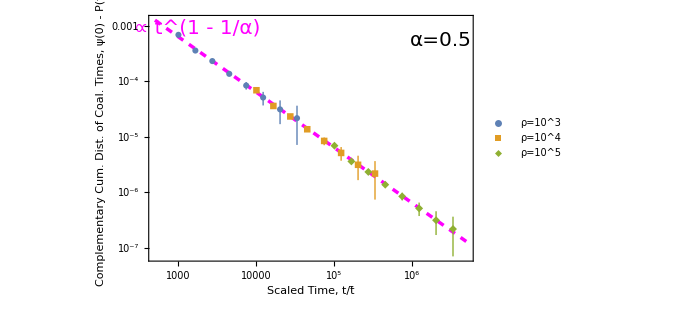

```mathematica
Module[{α=0.5, coal=.001, plotcdf, D =.5},
dummy= cdfsims[Select[#alpha == α && #coal < 10*coal &]];
dummy=dummy[All,<|#,"maxcdfrho1000"-> Max[dummy[Select[#coal == .001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho10000"-> Max[dummy[Select[#coal == .0001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho100000"-> Max[dummy[Select[#coal == .00001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdf"->KroneckerDelta[#coal,.001]*#maxcdfrho1000 + KroneckerDelta[#coal,.0001]*#maxcdfrho10000 + KroneckerDelta[#coal,.00001]*#maxcdfrho100000 |>&];
dummy=dummy[All,<|#,"compcdf"->#maxcdf -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
dummy= dummy[Select[#T < 50 &]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{.001, .0001, .00001}}];

Show[LogLogPlot[(3.141*((1/α -1)/(Gamma[1/α +1])))^-1*x^(1-1/α),{x,500,5000000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10^3", "10^4", "10^5"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1 - 1/α)",Magenta,20],Scaled[{.15,.95}]] },goodlabel["Scaled Time, t/t̄","Complementary Cum. Dist.
 of Coal. Times, ψ(0) - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
maxcdf
```

0.997837

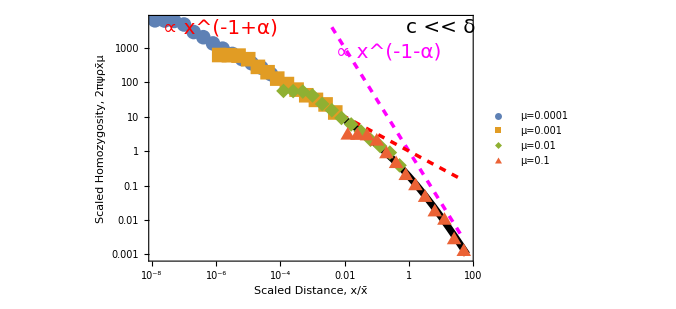

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦1;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal &&#c == .2&& #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[x^(-1+α),{x,.0001,50},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["∝ x^(-1+α)",Red,20],Scaled[{.22,.95}]], Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.74,.85}]], Text[Style["c << δ",Black,20],Scaled[{.9,.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, 2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

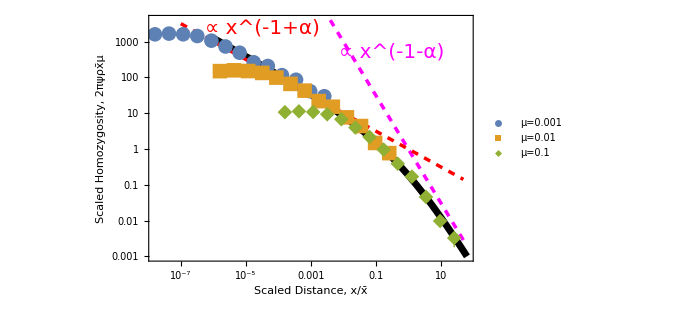

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal &&#c == 250&& #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[x^(-1+α),{x,.0000001,50},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["∝ x^(-1+α)",Red,20],Scaled[{.35,.95}]], Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.75,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, 2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

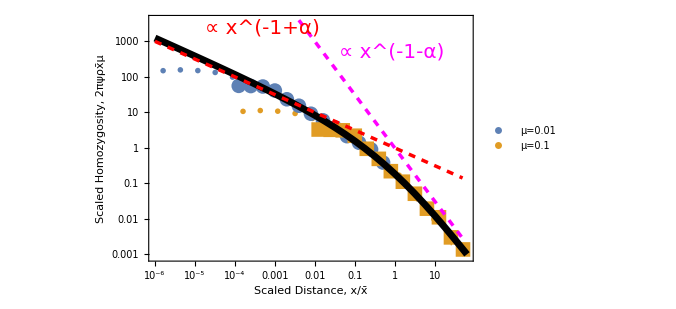

```mathematica
Module[{α=0.5,coal =.01, plotpoints,μvals=μlist⟦3;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#c ==250 &&#x0>0&]],{μ,μvals}];
plotpoints1 =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#c ==250 &&#x0>0&]],{μ,μvals}];
plotpoints2 =Table[{(#x0)/xscale[#mu,#alpha, #c^#alpha/2],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha, #c^#alpha/2]}&/@sims[Select[#alpha == α && #coal==coal &&#c ==.2&& #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[plotpoints,PlotMarkers->{"OpenMarkers",12},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],
ListLogLogPlot[plotpoints2,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>],ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,1},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[x^(-1+α),{x,.000001,50},PlotStyle->{Red,Dashed,Thickness[.005]}],
Epilog->{Text[Style["∝ x^(-1+α)",Red,20],Scaled[{.35,.95}]], Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.75,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, 2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

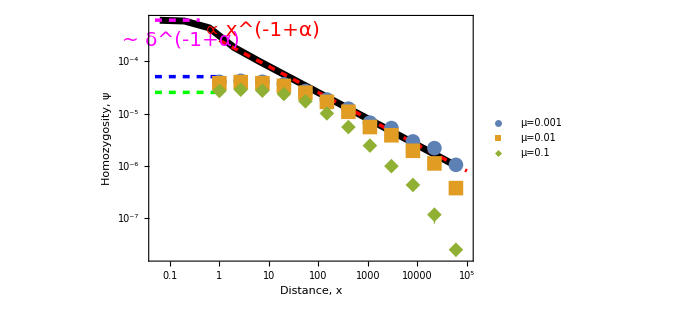

```mathematica
Module[{α=0.5,D = (250)^(.5)/2, coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},
xlist2=10^Range[-11,5,.5];
intvalsfinitedelta=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[(Cos[k x]*Exp[-.125*k^2/((D/.0001)^(1/.5))^2])/(1+k^α),{k,0,∞}],{x,xlist2}],{α,αlist⟦;;-2⟧}]];
plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #c==250&& #mu ==μ&&#x0>0&& #x0 < 100000&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x*(D/.0001)^(1/.5),intvalsfinitedelta[α][x]/(2*Pi*(D/.0001)^(1/.5)*coal^-1*.0001)},{x,Select[xlist2,#≤.00001&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,1},{10^-6,100}}],LogLogPlot[coal*(Gamma[1-.5]*Sin[3.141/4]/(2*3.141*D))*x^(-1+α),{x,1,100000},PlotStyle->{Red,Dashed,Thickness[.005]}],LogLogPlot[1/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*coal^-1*D*(.5)^(1-α)),{x,.05,.4},PlotStyle->{Magenta,Dashed,Thickness[.005]}],LogLogPlot[2*coal*Gamma[1+1/.5]/(250*Pi),{x,.05,1},PlotStyle->{Blue,Dashed,Thickness[.005]}],LogLogPlot[1*coal*Gamma[1+1/.5]/(250*Pi),{x,.05,1},PlotStyle->{Green,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style[" ∝ x^(-1+α) ",Red,20],Scaled[{.35,.94}]],Text[Style[" ~ δ^(-1+α) ",Magenta,20],Scaled[{.10,.9}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
Charting`ResolvePlotTheme[Automatic,Plot]
```

{GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],Method→{AxisPadding→Scaled[0.02],DefaultBoundaryStyle→Automatic,DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},DefaultMeshStyle→AbsolutePointSize[6],DefaultPlotStyle→{Directive[RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Directive[RGBColor[0.880722, 0.611041, 0.142051],AbsoluteThickness[1.6]],Directive[RGBColor[0.560181, 0.691569, 0.194885],AbsoluteThickness[1.6]],Directive[RGBColor[0.922526, 0.385626, 0.209179],AbsoluteThickness[1.6]],Directive[RGBColor[0.528488, 0.470624, 0.701351],AbsoluteThickness[1.6]],Directive[RGBColor[0.772079, 0.431554, 0.102387],AbsoluteThickness[1.6]],Directive[RGBColor[0.363898, 0.618501, 0.782349],AbsoluteThickness[1.6]],Directive[RGBColor[1, 0.75, 0],AbsoluteThickness[1.6]],Directive[RGBColor[0.647624, 0.37816, 0.614037],AbsoluteThickness[1.6]],Directive[RGBColor[0.571589, 0.586483, 0.],AbsoluteThickness[1.6]],Directive[RGBColor[0.915, 0.3325, 0.2125],AbsoluteThickness[1.6]],Directive[RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],AbsoluteThickness[1.6]],Directive[RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],AbsoluteThickness[1.6]],Directive[RGBColor[0.736782672705901, 0.358, 0.5030266573755369],AbsoluteThickness[1.6]],Directive[RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],AbsoluteThickness[1.6]]},DomainPadding→Scaled[0.02],RangePadding→Scaled[0.05]}}

```mathematica
clist
```

{0.2,250.}

```mathematica
lineStyledimensionful={Thick,Red,Dashed};
```

```mathematica
linedelta=Line[{{.01,.001},{.01,1}}];
```

```mathematica
linecp2=Line[{{.2,0},{.2,1}}];
```

```mathematica
linec250=Line[{{250,0},{250,1}}];
```

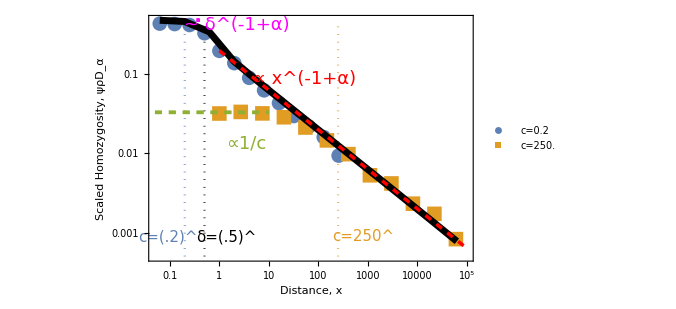

```mathematica
Module[{α=0.5,D = (250)^(.5)/2, coal =.01, plotpoints,cvals =clist[[;;]],μvals=μlist⟦2;;2⟧},
xlist2=10^Range[-11,5,.5];
intvalsfinitedelta=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[(Cos[k x]*Exp[-.125*k^2/((D/.0001)^(1/.5))^2])/(1+k^α),{k,0,∞}],{x,xlist2}],{α,αlist⟦;;-2⟧}]];
plotpoints =Table[{#x0,Around[#coal^-1*(#c)^(#alpha)/2*#hom,{#coal^-1*(#c)^(#alpha)/2*#dhomLow,#coal^-1*(#c)^(#alpha)/2*#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal &&  #mu ==.001&&   #c == c &&#x0>0&& #x0 < 100000&]],{c,cvals}];
Show[LogLogPlot[coal^-1*D/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*D*coal^-1*(.5)^(1-α)),{x,.05,.4},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ParametricPlot[{{Log[.5],Log[u]}},{u,.0005,.42},PlotStyle->{Black, Dotted}],ParametricPlot[{{Log[.2],Log[u]}},{u,.0005,.42},PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798], Dotted}],ParametricPlot[{{Log[250],Log[u]}},{u,.0005,.42},PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051], Dotted}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["c="<>ToString[#],20]&/@cvals,{.8,.9}]], ListLogLogPlot[Table[{x*(D/.0001)^(1/.5),coal^-1*D*intvalsfinitedelta[α][x]/(2*Pi*(D/.0001)^(1/.5)*coal^-1*.0001)},{x,Select[xlist2,#≤.00001&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,1},{10^-6,100}}],LogLogPlot[(Pi^2/6)*D*Gamma[1+1/.5]/(250*Pi),{x,.05,10},PlotStyle->{RGBColor[0.560181, 0.691569, 0.194885],Dashed,Thickness[.005]}],LogLogPlot[(Pi/6)*D*Gamma[1+1/.5]/(250),{x,.05,10},PlotStyle->{RGBColor[0.560181, 0.691569, 0.194885],Dashed,Thickness[.005]}],LogLogPlot[coal^-1*coal*(Gamma[1-.5]*Sin[3.141/4]/(2*3.141))*x^(-1+α),{x,1,100000},PlotStyle->{Red,Dashed,Thickness[.005]}],LogLogPlot[coal^-1*D/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*D*coal^-1*(.5)^(1-α)),{x,.05,.4},PlotStyle->{Magenta,Dashed,Thickness[.005]}],LogLogPlot[coal^-1*D/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*D*coal^-1*(.5)^(1-α)),{x,.05,.4},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
Epilog->{Text[Style[" ∝ x^(-1+α) ",Red,18],Scaled[{.48,.74}]],Text[Style[" ∝1/c ",RGBColor[0.560181, 0.691569, 0.194885],18],Scaled[{.30,.48}]],Text[Style[" ~ δ^(-1+α) ",Magenta,18],Scaled[{.27,.96}]],Text[Style[" δ=(.5)^ ",Black,15],Scaled[{.24,.1}]],Text[Style[" c=(.2)^ ",RGBColor[0.368417, 0.506779, 0.709798],15],Scaled[{.06,.1}]],Text[Style[" c=250^ ",RGBColor[0.880722, 0.611041, 0.142051],15],Scaled[{.66,.1}]],Directive[lineStyledimensionful], linedelta},goodlabel["Distance, x","Scaled Homozygosity, ψρD_α",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

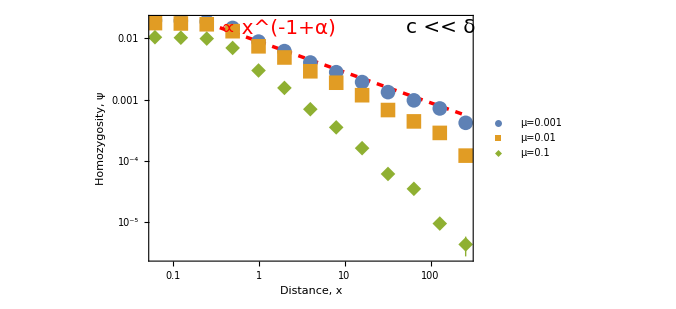

```mathematica
Module[{α=0.5,D = (.2)^(.5)/2, coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #c==.2&& #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[LogLogPlot[coal*(Gamma[1-.5]*Sin[3.141/4]/(2*3.141*D))*x^(-1+α),{x,.25,265},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style[" ∝ x^(-1+α) ",Red,20],Scaled[{.4,.95}]], Text[Style["c << δ",Black,20],Scaled[{.9,.95}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

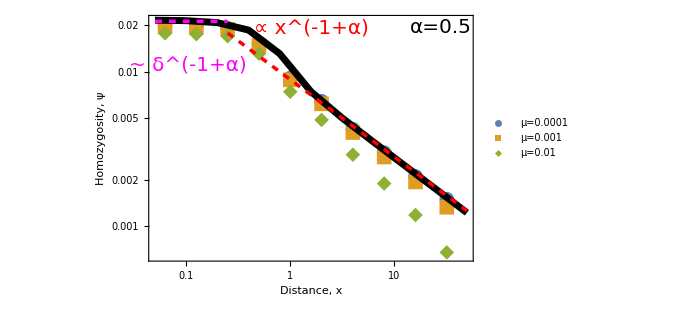

```mathematica
Module[{α=0.5,D = (.2)^(.5)/2, coal =.01, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #c==.2&& #mu ==μ&&#x0>0&&#x0<50&]],{μ,μvals}];
xlist2=10^Range[-8,0,.3];
intvalsfinitedelta=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[(Cos[k x]*Exp[-.125*k^2/((D/.0001)^(1/.5))^2])/(1+k^α),{k,0,∞}],{x,xlist2}],{α,αlist⟦;;-2⟧}]];
Show[
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],ListLogLogPlot[Table[{x*(D/.0001)^(1/.5),intvalsfinitedelta[α][x]/(2*Pi*(D/.0001)^(1/.5)*coal^-1*.0001)},{x,Select[xlist2,#≤.00001&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,1},{10^-6,10}}], LogLogPlot[coal*(Gamma[1-.5]*Sin[3.141/4]/(2*3.141*D))*x^(-1+α),{x,.25,50},PlotStyle->{Red,Dashed,Thickness[.005]}],  LogLogPlot[1/( 1 + Pi*(2^(3.5/2)/Gamma[.25])*coal^-1*D*(.5)^(1-α)),{x,.05,.25},PlotStyle->{Magenta,Dashed,Thickness[.005]}],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]],Text[Style[" ∝ x^(-1+α) ",Red,20],Scaled[{.5,.95}]],Text[Style[" ~ δ^(-1+α) ",Magenta,20],Scaled[{.12,.8}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
μlist[[2;;3]]
```

{0.001,0.01}

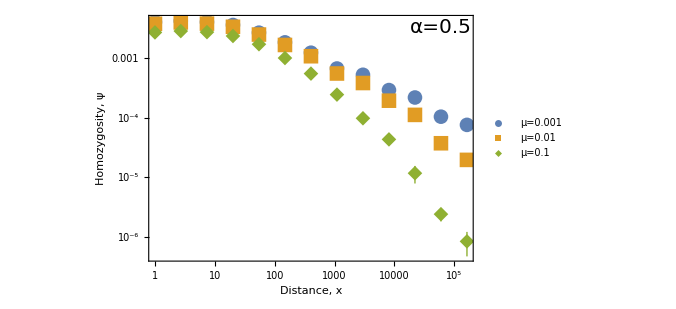

```mathematica
Module[{α=0.5,coal =1, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=0.5",20],Scaled[{.9,.95}]]},goodlabel["Distance, x","Homozygosity, ψ",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False ]]
```

## α=.75

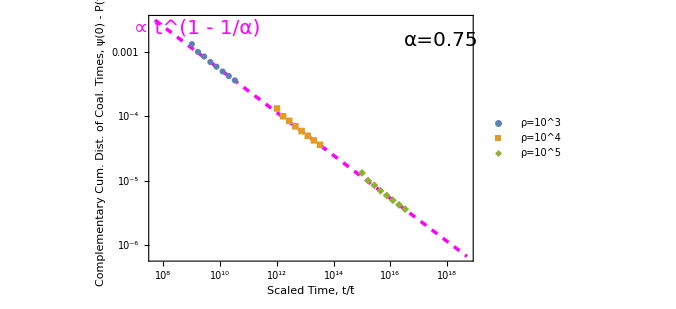

```mathematica
Module[{α=0.75, coal=.001, plotcdf, c =1, D =.5},
dummy= cdfsims[Select[#alpha == α && #coal < 10*coal &]];
dummy=dummy[All,<|#,"maxcdfrho1000"-> Max[dummy[Select[#coal == .001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho10000"-> Max[dummy[Select[#coal == .0001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdfrho100000"-> Max[dummy[Select[#coal == .00001  &],"cdf"]]|>&];
dummy=dummy[All,<|#,"maxcdf"->KroneckerDelta[#coal,.001]*#maxcdfrho1000 + KroneckerDelta[#coal,.0001]*#maxcdfrho10000 + KroneckerDelta[#coal,.00001]*#maxcdfrho100000 |>&];
dummy=dummy[All,<|#,"compcdf"->#maxcdf -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
dummy= dummy[Select[#T < 50 &]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{.001, .0001, .00001}}];

Show[LogLogPlot[(3.141*((1/α -1)/(Gamma[1/α +1])))^-1*x^(1-1/α),{x,50000000,5000000000000000000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10^3", "10^4", "10^5"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=0.75",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1 - 1/α)",Magenta,20],Scaled[{.15,.95}]] },goodlabel["Scaled Time, t/t̄","Complementary Cum. Dist.
 of Coal. Times, ψ(0) - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

## α=1

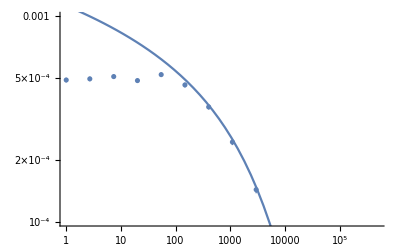

```mathematica
Module[{α=1.0, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[.05fLT[x,μ,α],{x,1, 5 10^5}],
PlotRange->{All,{-4,-3}Log[10]}]]
```

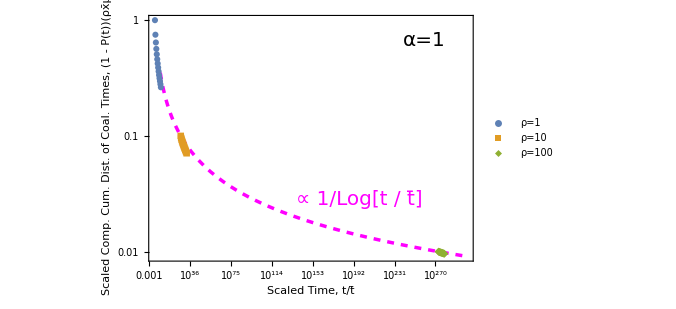

```mathematica
Module[{α=1.00, coal=1, plotcdf, c = 1,D =1},
dummy= cdfsims[Select[#alpha == α && #coal ≥ .001*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(D*Exp[2*Pi/#coal])*#T|>&];
dummy=dummy[All,<|#,"scaledcompcdf"->#coal*#compcdf/(D)|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#coal*#dcdfLow/(D)|>&];
dummy= dummy[All,<|#,"scaleddcdfHigh"->#coal*#dcdfHigh/(D)|>&];
dummy= dummy[Select[#T < 500000&]];
plotcdf = dummy;
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{ 1, .1, .01}}];



Show[LogLogPlot[2*Pi/Log[x],{x,10^1,10^300},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{ "1", "10", "100"},Scaled[{.12,.2}]]],Epilog->{Text[Style["α=1",20],Scaled[{.85,.9}]],Text[Style["∝ 1/Log[t / t̄]",Magenta,20],Scaled[{.65,.25}]], ImageSize->500 },goodlabel["Scaled Time, t/t̄","Scaled Comp. Cum. Dist. of
 Coal. Times, (1 - P(t))(ρx̄μ)^-1",20],FrameStyle->Directive[20,Black],ImageSize->500,
PlotRange->All,Axes->False]]
```

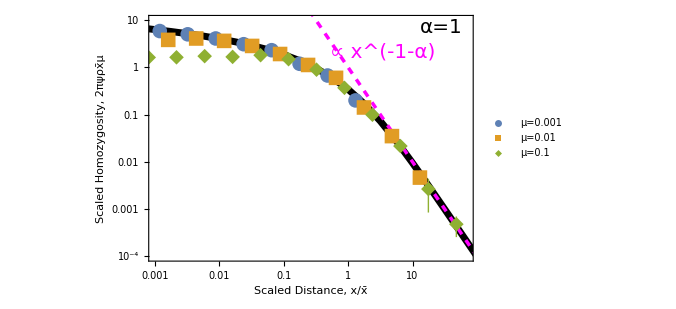

```mathematica
Module[{α=1.0,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧,yscale=80000},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.001,70},{10^-4,10}}] ,
LogLogPlot[x^(-1-α),{x,.001,500},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.72,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

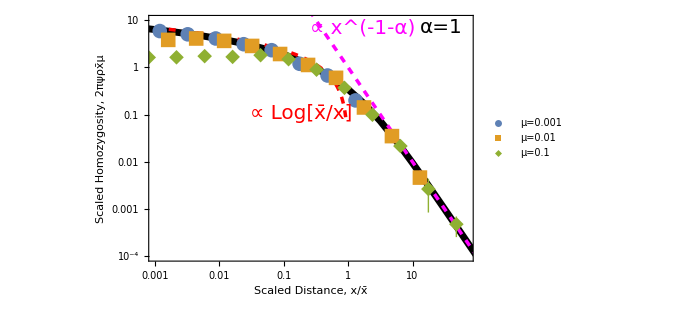

```mathematica
Module[{α=1.0,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧,yscale=80000},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.001,70},{10^-4,10}}], LogLogPlot[Log[1/x],{x,.001,5},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
LogLogPlot[x^(-1-α),{x,.001,500},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.66,.95}]], Text[Style["∝ Log[x̄/x]",Red,20],Scaled[{0.47,.6}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, 2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α = 1.25

```mathematica
250^1.25/2
```

497.044

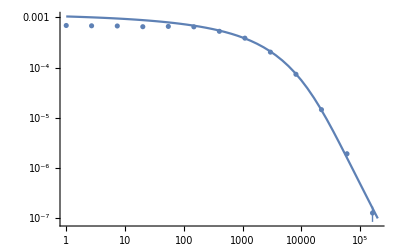

```mathematica
Module[{α=1.25, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 2 10^5}],PlotRange->All]]
```

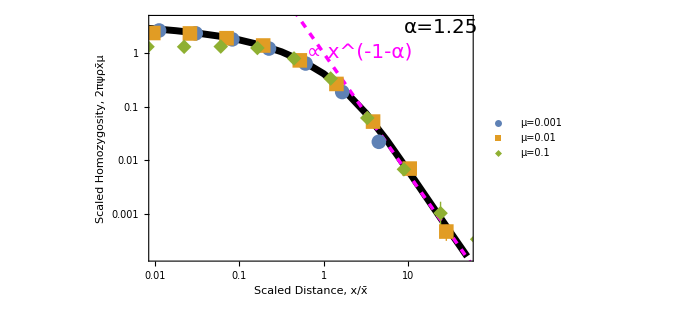

```mathematica
Module[{α=1.25,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-3.8,All}}],
LogLogPlot[x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.65,.85}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, 2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

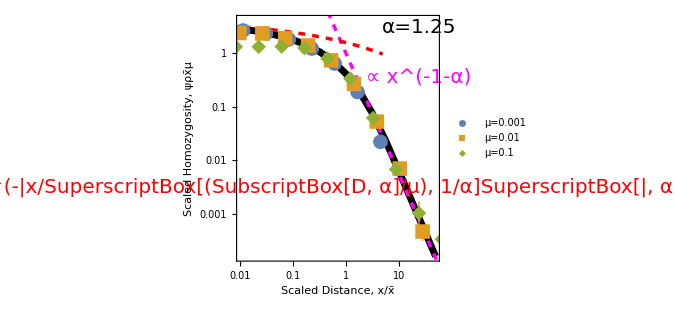

```mathematica
Module[{α=1.25,coal =.01,D=250^2/2, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-3.8,All}}],
LogLogPlot[x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[2*Pi*Exp[-x^(α-1)]/(2*α*Sin[Pi/α]),{x,.001,5},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.25",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.5,.3}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity, ψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=1.45

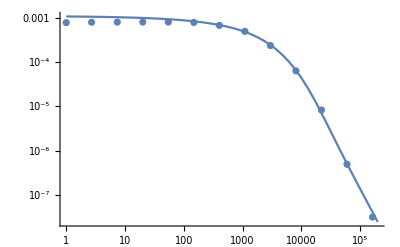

```mathematica
Module[{α=1.45, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 2 10^5}],
PlotRange->All]]
```

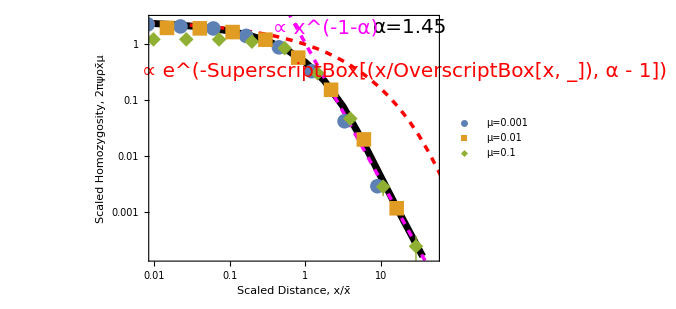

```mathematica
Module[{α=1.45,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-3.8,All}}],
LogLogPlot[x^(-1-α),{x,.1,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}], LogLogPlot[2*Pi*Exp[-x^(α-1)]/(2*α*Sin[Pi/α]),{x,.001,5000},PlotStyle->{Red,Dashed,Thickness[.005]}] ,
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.45",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.61,.95}]], Text[Style["∝ e^(-SuperscriptBox[(x/OverscriptBox[x, _]), α - 1])",Red,20],Scaled[{0.88,.77}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

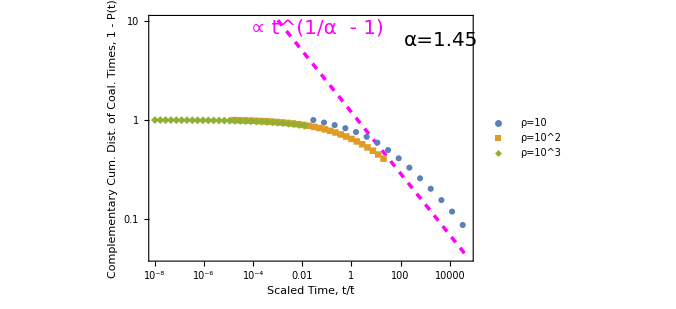

```mathematica
Module[{α=1.45, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[(α*Sin[Pi/α])*x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.45",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.52,.95}]] },goodlabel["Scaled Time, t/t̄","Complementary Cum. Dist.
 of Coal. Times, 1 - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

## α=1.65

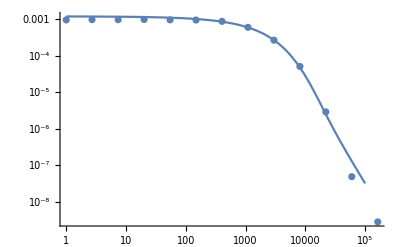

```mathematica
Module[{α=1.65, coal=0.1, μ = 0.01, plotds},plotds = sims[Select[#alpha == α && #coal==coal && #mu ==μ&]];
Show[ListLogLogPlot[{#x0,Around[#hom,{#dhomLow,#dhomHigh}]}&/@plotds],
LogLogPlot[coeff[coal,μ,α]fLT[x,μ,α],{x,1, 10^5}],
PlotRange->All]]
```

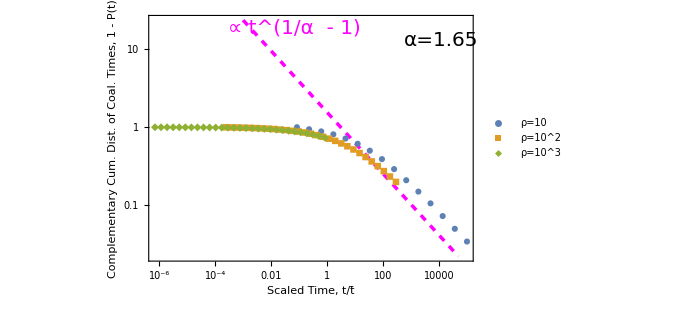

```mathematica
Module[{α=1.65, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[(α*Sin[Pi/α])*x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.45,.95}]] },goodlabel["Scaled Time, t/t̄","Complementary Cum. Dist.
 of Coal. Times, 1 - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

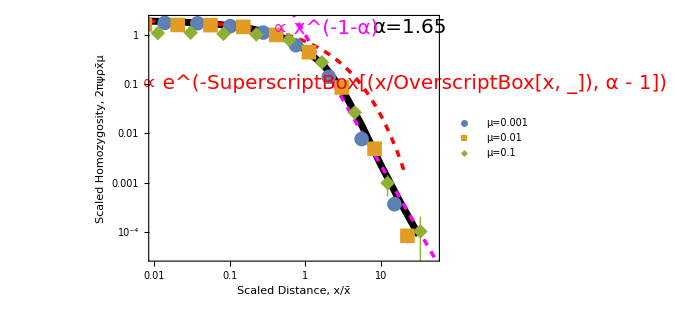

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤3*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-4.5,All}}], LogLogPlot[2*Pi*Exp[-x^(α-1)]/(2*α*Sin[Pi/α]),{x,.001,20},PlotStyle->{Red,Dashed,Thickness[.005]}],
LogLogPlot[x^(-1-α),{x,.01,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.95}]], Text[Style["∝ e^(-SuperscriptBox[(x/OverscriptBox[x, _]), α - 1])",Red,20],Scaled[{0.88,.72}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],Scaled[{0.61,0.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

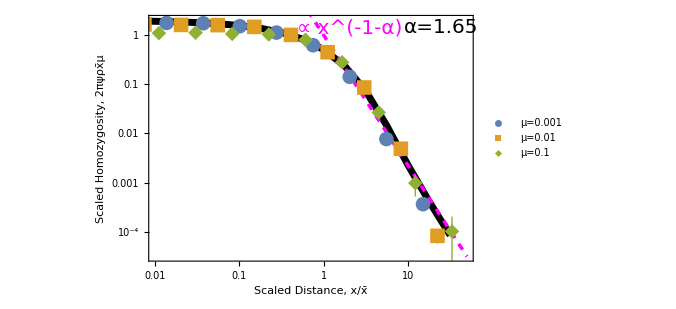

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤1000*xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-4.5,All}}],
LogLogPlot[x^(-1-α),{x,.01,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],Scaled[{.9,.95}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],Scaled[{0.62,0.95}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

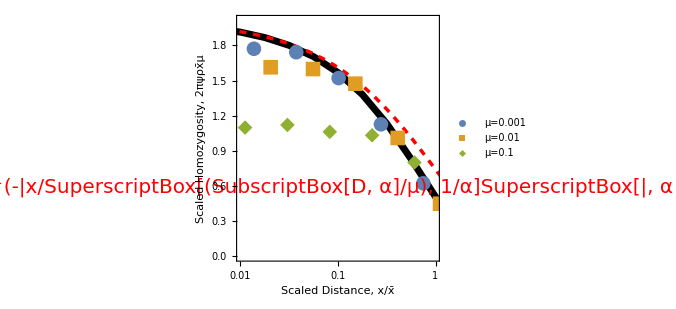

```mathematica
Module[{α=1.65,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLinearPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,1},{10^-6,All}}], LogLinearPlot[2*Pi*Exp[-x^(α-1)]/(2*α*Sin[Pi/α]),{x,.0001,10},PlotStyle->{Red,Dashed,Thickness[.005]}],
LogPlot[x^(-1-α),{x,.01,200},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLinearPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.65",20],{3,1}], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.5,.3}]],Text[Style["  ∝ x^(-1-α)",Magenta,20],{0.6,0.8}]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=1.85

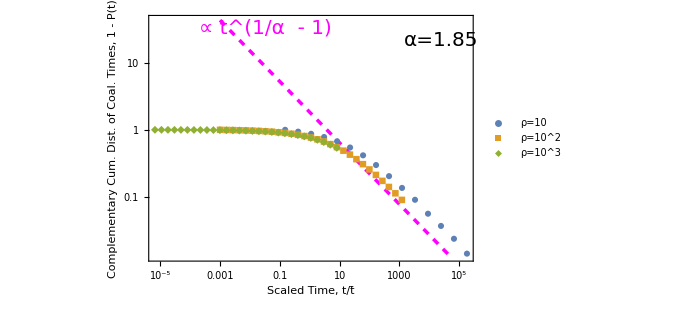

```mathematica
Module[{α=1.85, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-α)*D)^(1/(1 - α))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[(α*Sin[Pi/α])*x^(1/α-1),{x,.001,50000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=1.85",20],Scaled[{.9,.9}]],Text[Style["∝ t^(1/α  - 1)",Magenta,20],Scaled[{.36,.95}]] },goodlabel["Scaled Time, t/t̄","Complementary Cum. Dist.
 of Coal. Times, 1 - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

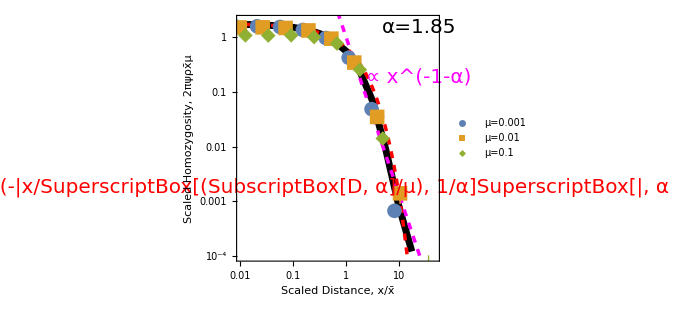

```mathematica
Module[{α=1.85,coal =.01, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/xscale[#mu,#alpha],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,#alpha]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},
PlotRange->{{.01,50},{10^-4,2}}],
LogLogPlot[x^(-1-α),{x,.01,50},PlotStyle->{Magenta,Dashed,Thickness[.005]}],LogLogPlot[2*Pi*Exp[-x^(α-1)]/(2*α*Sin[Pi/α]),{x,.001,500000},PlotStyle->{Red,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.85",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{0.9,.75}]], Text[Style["∝ e^(-|x/SuperscriptBox[(SubscriptBox[D, α]/μ), 1/α]SuperscriptBox[|, α - 1])",Red,20],Scaled[{0.48,.3}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  2πψρx̄μ",20],FrameStyle->Directive[20,Black], ImageSize->500]]
```

## α=2.05 (F distribution)

Null

```mathematica
df =0.5Module[{α=2.05},Moment[FRatioDistribution[2α,2α],2]]
```

59.5476

```mathematica
250^2.05/2
```

41185.8

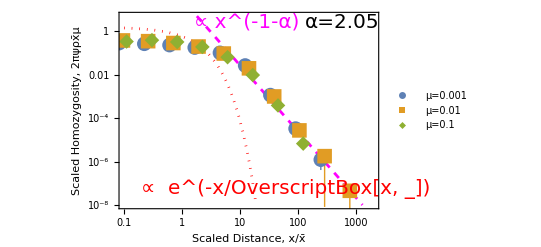

```mathematica
Module[{α=2.05,coal =.01,D=250^2/2, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/(√(df/#mu)),Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,2.00,df]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[LogLogPlot[{30*x^(-1-α),2*Pi*Exp[-x]/(4)},{x,.1,2000},PlotStyle->{{Magenta,Dashed,Thickness[.005]},{Red,Dotted,Thickness[.005]}},PlotRange->{{.1,2000},{10^-8,5}}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=2.05",20],Scaled[{.86,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.49,0.95}]],
Text[Style["  ∝  e^(-x/OverscriptBox[x, _])",Red,20],Scaled[{.64,.1}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  2πψρx̄μ",20],FrameStyle->Directive[20,Black]]]
```

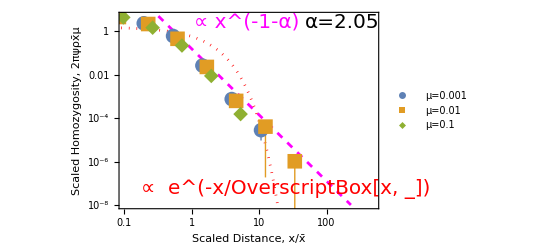

```mathematica
Module[{α=2.05,coal =.01,D=250^2/2, plotpoints,μvals=μlist⟦2;;4⟧},plotpoints =Table[{(#x0)/(√(D/#mu)),Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscale[#coal,#mu,2.00,D]}&/@sims[Select[#alpha == α && #coal==coal && #mu ==μ&&#x0>0&& #x0<80000&]],{μ,μvals}];
Show[LogLogPlot[{(2*Pi)^-1*x^(-1-α),2*Pi*Exp[-x]/(4)},{x,.0001,500},PlotStyle->{{Magenta,Dashed,Thickness[.005]},{Red,Dotted,Thickness[.005]}},PlotRange->{{.1,500},{10^-8,5}}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=2.05",20],Scaled[{.86,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.49,0.95}]],
Text[Style["  ∝  e^(-x/OverscriptBox[x, _])",Red,20],Scaled[{.64,.1}]]},goodlabel["Scaled Distance, x/x̄","Scaled Homozygosity,  2πψρx̄μ",20],FrameStyle->Directive[20,Black]]]
```

## All

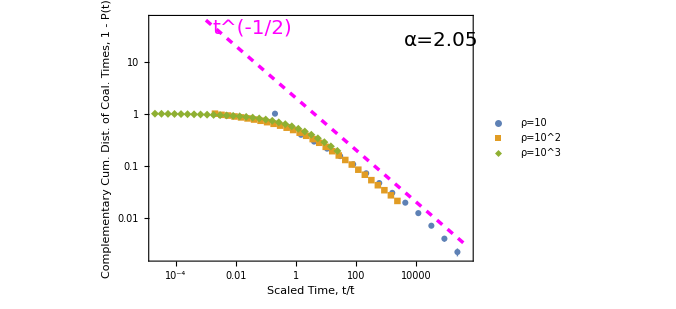

```mathematica
Module[{α=2.05, coal=.01, plotcdf, c =5, D =2.5},
dummy= cdfsims[Select[#alpha == α && #coal <= 100*coal &]];
maxcdf = Max[dummy[All,"cdf"]];
dummy=dummy[All,<|#,"compcdf"->1 -#cdf|>&];
dummy=dummy[All,<|#,"scaledT"->(2*#coal^(-2)*D)^(1/(1 - 2))*#T|>&];
dummy=dummy[All,<|#,"scaleddcdfLow"->#dcdfLow|>&];

dummy= dummy[All,<|#,"scaleddcdfHigh"->#dcdfHigh|>&];
plotcdf = dummy;
dummy=dummy[All,<|#,"scaledcompcdf"->#compcdf|>&];
plotpoints =Table[{#scaledT,Around[#scaledcompcdf,{#scaleddcdfHigh,#scaleddcdfLow}]}&/@dummy[Select[#alpha == α && #coal==coal &]],{coal,{1,.1,.01 }}];

Show[LogLogPlot[(2*Sin[Pi/2])*x^(-1/2),{x,.001,500000},PlotStyle->{Magenta,Dashed,Thickness[.005]}],ListLogLogPlot[plotpoints ,
PlotRange->All,PlotMarkers->Automatic,IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["ρ="<>ToString[#],20]&/@{"10", "10^2", "10^3"},Scaled[{.2,.3}]]],Epilog->{Text[Style["α=2.05",20],Scaled[{.9,.9}]],Text[Style["t^(-1/2)",Magenta,20],Scaled[{.32,.95}]] },goodlabel["Scaled Time, t/t̄","Complementary Cum. Dist.
 of Coal. Times, 1 - P(t)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

```mathematica
lineStyle={Thick,Black,Dashed};
```

```mathematica
lineStyle2={Thick, Black};
```

```mathematica
lineStyle3={Thick, Blue};
```

```mathematica
lineStyle4={Thick,Green};
```

```mathematica
lineStyle5={Thick,Red};
```

```mathematica
lineStyle6={Thick,Purple};
```

```mathematica
lineStyle7={Thick,Yellow};
```

```mathematica
lineStyle8={Thick,White};
```

```mathematica
line99=Line[{{-.5,0},{-.5,2}}];
```

```mathematica
line0=Line[{{0,0},{0,2}}];
```

```mathematica
line1=Line[{{1,0},{1,1}}];
```

```mathematica
line2=Line[{{2,0},{2,1}}];
```

```mathematica
line3=Line[{{3,0},{3,2}}];
```

```mathematica
line999=Line[{{-.5,0},{-.5,2}}];
```

```mathematica
line00=Line[{{0,0},{0,2}}];
```

```mathematica
line11=Line[{{1,1},{1,2}}];
```

```mathematica
line22=Line[{{2,0},{2,2}}];
```

```mathematica
line33=Line[{{3,0},{3,2}}];
```

```mathematica
line44=Line[{{0,2},{3,2}}];
```

```mathematica
line55=Line[{{0,0},{3,0}}];
```

```mathematica
line66=Line[{{0,1},{3,1}}];
```

```mathematica
line77=Line[{{0,.5},{1,.5}}];
```

```mathematica
line88=Line[{{0,.5},{3,.5}}];
```

```mathematica
line999=Line[{{-.5,0},{-.5,-2}}];
```

```mathematica
line000=Line[{{0,0},{0,-2}}];
```

```mathematica
line111=Line[{{1,0},{1,-1}}];
```

```mathematica
line222=Line[{{2,0},{2,-1}}];
```

```mathematica
line333=Line[{{3,0},{3,-2}}];
```

```mathematica
line444=Line[{{0,-2},{3,-2}}];
```

```mathematica
line555=Line[{{0,0},{3,0}}];
```

```mathematica
line666=Line[{{0,-1},{3,-1}}];
```

```mathematica
line777=Line[{{0,.3},{1,.3}}];
```

```mathematica
line888=Line[{{0,.3},{3,.3}}];
```

```mathematica
line999=Line[{{0,0},{3,0}}];
```

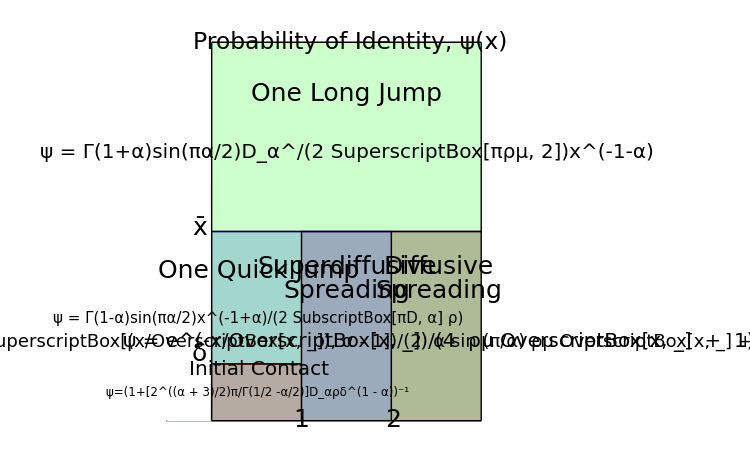

```mathematica
Show[Plot[{0, UnitStep[x] ,2*UnitStep[x] , .3*UnitStep[x] -.3*UnitStep[x -1],  UnitStep[x -1] - UnitStep[x -4],  UnitStep[x -2],UnitStep[x -3]},{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4], Directive[lineStyle5],Directive[lineStyle6],Directive[lineStyle7], Directive[lineStyle8],Directive[lineStyle8]},Epilog->{Directive[lineStyle2],Text[Style["1",Black,25],Scaled[{.43,.020}]],Text[Style["2",Black,25],Scaled[{.71,.020}]], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,25],Scaled[{.57,.85}]],Text[Style["ψ = Γ(1+α)sin(πα/2)D_α^/(2 SuperscriptBox[πρμ, 2])x^(-1-α)",Black,20],Scaled[{.57,.70}]],  Text[Style["Superdiffusive",Black,25],Scaled[{.57,.41}]], Text[Style[" Spreading",Black,25],Scaled[{.57,.35}]],Text[Style["ψ=e^(-SuperscriptBox[(x/OverscriptBox[x, _]), α - 1])/(2  α sin (π/α) ρμ OverscriptBox[x, _] + 1)",Black,18],Scaled[{.57,.22}]], Text[Style["One Quick Jump",Black,25],Scaled[{.3,.40}]],Text[Style["ψ = Γ(1-α)sin(πα/2)x^(-1+α)/(2 SubscriptBox[πD, α] ρ)",Black,15],Scaled[{.30,.28}]] ,Text[Style["ψ=(1+[2^((α + 3)/2)π/Γ(1/2 -α/2)]D_αρδ^(1 - α))^-1",Black,11.9],Scaled[{.296,.09}]],Text[Style["Initial Contact",Black,20],Scaled[{.30,.15}]] ,Text[Style[" ψ = e^(-x/OverscriptBox[x, _])/(4  ρμ OverscriptBox[x, _]  +  1)",Black,20],Scaled[{.85,.22}]], Text[Style["Probability of Identity, ψ(x) ",Black,23.5],Scaled[{.58,.98}]],Text[Style["Diffusive",Black,25],Scaled[{.85,.41}]],Text[Style[" Spreading",Black,25],Scaled[{.85,.35}]],line0, line1, line2, line3, line44, line66, line777, line999}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

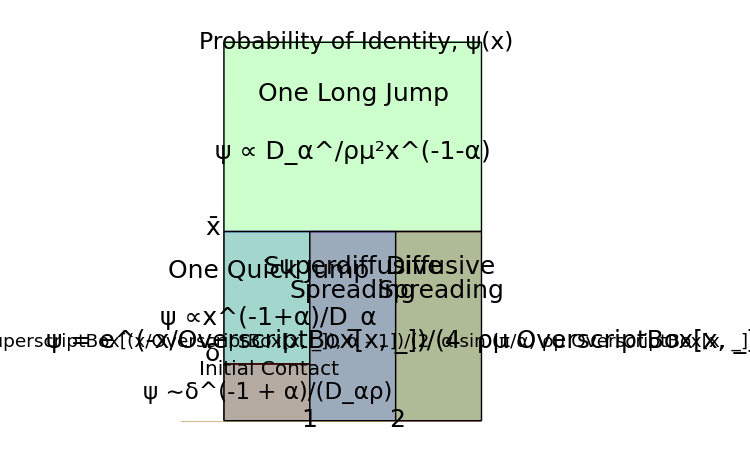

```mathematica
Show[Plot[{0, UnitStep[x] ,2*UnitStep[x] , .3*UnitStep[x] -.3*UnitStep[x -1],  UnitStep[x -1] - UnitStep[x -4],  UnitStep[x -2],UnitStep[x -3]},{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4], Directive[lineStyle5],Directive[lineStyle6],Directive[lineStyle7], Directive[lineStyle8],Directive[lineStyle8]},Epilog->{Directive[lineStyle2],Text[Style["1",Black,25],Scaled[{.43,.020}]],Text[Style["2",Black,25],Scaled[{.71,.020}]], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,25],Scaled[{.57,.85}]],Text[Style["ψ ∝ D_α^/ρμ^2x^(-1-α)",Black,25],Scaled[{.57,.70}]],  Text[Style["Superdiffusive",Black,25],Scaled[{.57,.41}]], Text[Style[" Spreading",Black,25],Scaled[{.57,.35}]],Text[Style["ψ=e^(-SuperscriptBox[(x/OverscriptBox[x, _]), α - 1])/(2  α sin (π/α) ρμ OverscriptBox[x, _] + 1)",Black,18.5],Scaled[{.57,.22}]], Text[Style["ψ ∝x^(-1+α)/D_α",Black,25],Scaled[{.30,.28}]]  ,Text[Style["One Quick Jump",Black,25],Scaled[{.3,.40}]],Text[Style["ψ ∼δ^(-1 + α)/(D_αρ)",Black,23],Scaled[{.296,.09}]],Text[Style["Initial Contact",Black,20],Scaled[{.30,.15}]] ,Text[Style[" ψ = e^(-x/OverscriptBox[x, _])/(4  ρμ OverscriptBox[x, _]  +  1)",Black,25],Scaled[{.85,.22}]], Text[Style["Probability of Identity, ψ(x) ",Black,23.5],Scaled[{.58,.98}]],Text[Style["Diffusive",Black,25],Scaled[{.85,.41}]],Text[Style[" Spreading",Black,25],Scaled[{.85,.35}]],line0, line1, line2, line3, line44, line66, line777, line999}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

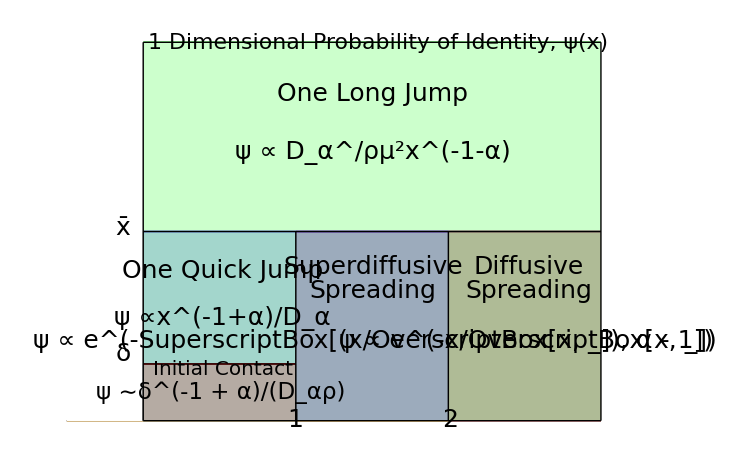

```mathematica
Show[Plot[{0, UnitStep[x] ,2*UnitStep[x] , .3*UnitStep[x] -.3*UnitStep[x -1],  UnitStep[x -1] - UnitStep[x -4],  UnitStep[x -2],UnitStep[x -3]},{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4], Directive[lineStyle5],Directive[lineStyle6],Directive[lineStyle7], Directive[lineStyle8],Directive[lineStyle8]},Epilog->{Directive[lineStyle2],Text[Style["1",Black,25],Scaled[{.43,.020}]],Text[Style["2",Black,25],Scaled[{.71,.020}]], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,25],Scaled[{.57,.85}]],Text[Style["ψ ∝ D_α^/ρμ^2x^(-1-α)",Black,25],Scaled[{.57,.70}]],  Text[Style["Superdiffusive",Black,25],Scaled[{.57,.41}]], Text[Style[" Spreading",Black,25],Scaled[{.57,.35}]],Text[Style["ψ ∝ e^(-SuperscriptBox[(x/OverscriptBox[x, _]), α - 1])",Black,25],Scaled[{.57,.22}]], Text[Style["ψ ∝x^(-1+α)/D_α",Black,25],Scaled[{.30,.28}]]  ,Text[Style["One Quick Jump",Black,25],Scaled[{.3,.40}]],Text[Style["ψ ∼δ^(-1 + α)/(D_αρ)",Black,23],Scaled[{.296,.09}]],Text[Style["Initial Contact",Black,20],Scaled[{.30,.15}]] ,Text[Style[" ψ ∝ e^(-x/OverscriptBox[x, _])",Black,25],Scaled[{.85,.22}]], Text[Style["1 Dimensional Probability of Identity, ψ(x) ",Black,22],Scaled[{.58,.98}]],Text[Style["Diffusive",Black,25],Scaled[{.85,.41}]],Text[Style[" Spreading",Black,25],Scaled[{.85,.35}]],line0, line1, line2, line3, line44, line66, line777, line999}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

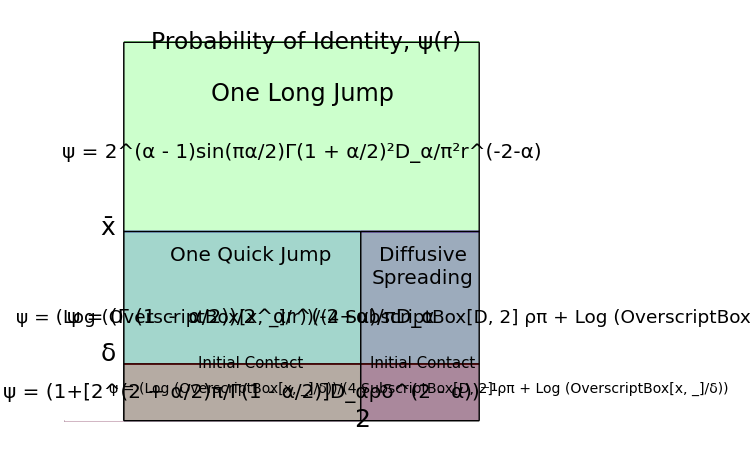

```mathematica
Show[Plot[{0, UnitStep[x],2*UnitStep[x]-2*UnitStep[x-3], .3*UnitStep[x], UnitStep[x -2], 0, 0    },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4],Directive[lineStyle5],Directive[lineStyle6], Directive[lineStyle8], Directive[lineStyle8]  },Epilog->{Directive[lineStyle2], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,24],Scaled[{.57,.85}]],Text[Style["ψ = 2^(α - 1)sin(πα/2)Γ(1 + α/2)^2D_α/π^2r^(-2-α) ",Black,20],Scaled[{.57,.70}]],   Text[Style["One Quick Jump",Black,20],Scaled[{.45,.44}]],Text[Style["ψ = (Γ (1  -  α/2))/2^αr^(-2+α)/πD_α",Black,20],Scaled[{.45,.28}]], Text[Style["ψ = (1+[2^(2 + α/2)π/Γ(1 - α/2)]D_αρδ^(2 - α))^-1",Black,20],Scaled[{.45,.09}]],Text[Style["ψ = (Log (OverscriptBox[x, _]/r))/(4 SubscriptBox[D, 2] ρπ + Log (OverscriptBox[x, _]/δ))",Black,18.5],Scaled[{.85,.28}]], Text[Style["Diffusive",Black,20],Scaled[{.85,.44}]],Text[Style["Spreading",Black,20],Scaled[{.85,.38}]], Text[Style["Initial Contact",Black,15],Scaled[{.45,.165}]],Text[Style[" ψ = (Log (OverscriptBox[x, _]/δ))/(4 SubscriptBox[D, 2] ρπ + Log (OverscriptBox[x, _]/δ))",Black,14],Scaled[{.84,.1}]],Text[Style["Initial Contact",Black,15],Scaled[{.85,.165}]],Text[Style[" 2 ",Black,25],Scaled[{.71,.020}]], Text[Style["Probability of Identity, ψ(r) ",Black,23.5],Scaled[{.58,.98}]],line0, line2, line3, line44, line55, line66, line888}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

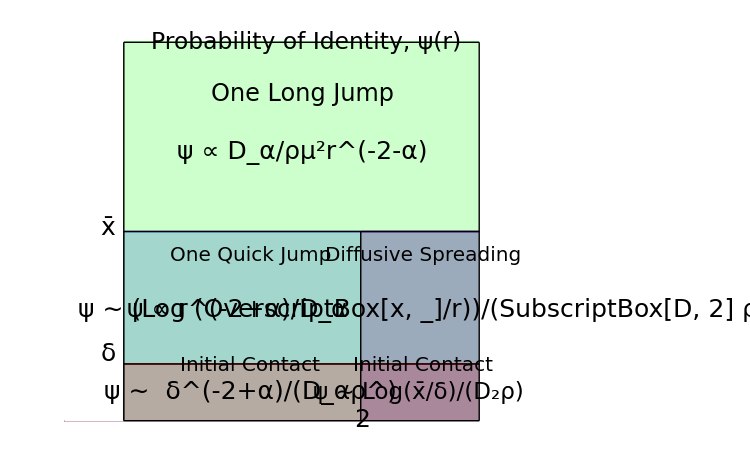

```mathematica
Show[Plot[{0, UnitStep[x],2*UnitStep[x]-2*UnitStep[x-3], .3*UnitStep[x], UnitStep[x -2], 0, 0    },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4],Directive[lineStyle5],Directive[lineStyle6], Directive[lineStyle8], Directive[lineStyle8]  },Epilog->{Directive[lineStyle2], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,24],Scaled[{.57,.85}]],Text[Style["ψ ∝ D_α/ρμ^2r^(-2-α) ",Black,25],Scaled[{.57,.70}]],   Text[Style["One Quick Jump",Black,20],Scaled[{.45,.44}]],Text[Style["ψ ∝ r^(-2+α)/D_α",Black,25],Scaled[{.42,.3}]], Text[Style["ψ ∼  δ^(-2+α)/(D_αρ^)",Black,25],Scaled[{.45,.09}]],Text[Style["ψ ∼ (Log (OverscriptBox[x, _]/r))/(SubscriptBox[D, 2] ρ)",Black,25],Scaled[{.85,.3}]], Text[Style["Diffusive Spreading",Black,20],Scaled[{.85,.44}]], Text[Style["Initial Contact",Black,20],Scaled[{.45,.16}]],Text[Style[" ψ ∼ Log(x̄/δ)/(D_2ρ)",Black,23],Scaled[{.84,.09}]],Text[Style["Initial Contact",Black,20],Scaled[{.85,.16}]],Text[Style[" 2 ",Black,25],Scaled[{.71,.020}]], Text[Style["Probability of Identity, ψ(r) ",Black,23.5],Scaled[{.58,.98}]],line0, line2, line3, line44, line55, line66, line888}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

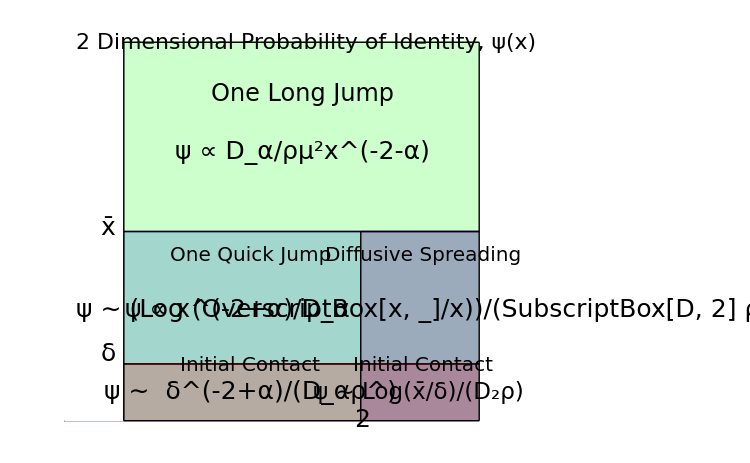

```mathematica
Show[Plot[{0, UnitStep[x],2*UnitStep[x]-2*UnitStep[x-3], .3*UnitStep[x], UnitStep[x -2], 0, 0    },{x,-.5 ,3 }, LabelStyle->Directive[Bold, Black],PlotStyle->{Directive[lineStyle2],Directive[lineStyle3],Directive[lineStyle4],Directive[lineStyle5],Directive[lineStyle6], Directive[lineStyle8], Directive[lineStyle8]  },Epilog->{Directive[lineStyle2], 
Text[Style["x̄",Black,25],Scaled[{.12,.51}]],Text[Style["δ",Black,25],Scaled[{.12,.19}]], Text[Style["One Long Jump",Black,24],Scaled[{.57,.85}]],Text[Style["ψ ∝ D_α/ρμ^2x^(-2-α) ",Black,25],Scaled[{.57,.70}]],   Text[Style["One Quick Jump",Black,20],Scaled[{.45,.44}]],Text[Style["ψ ∝ x^(-2+α)/D_α",Black,25],Scaled[{.42,.3}]], Text[Style["ψ ∼  δ^(-2+α)/(D_αρ^)",Black,25],Scaled[{.45,.09}]],Text[Style["ψ ∼ (Log (OverscriptBox[x, _]/x))/(SubscriptBox[D, 2] ρ)",Black,25],Scaled[{.85,.3}]], Text[Style["Diffusive Spreading",Black,20],Scaled[{.85,.44}]], Text[Style["Initial Contact",Black,20],Scaled[{.45,.16}]],Text[Style[" ψ ∼ Log(x̄/δ)/(D_2ρ)",Black,23],Scaled[{.84,.09}]],Text[Style["Initial Contact",Black,20],Scaled[{.85,.16}]],Text[Style[" 2 ",Black,25],Scaled[{.71,.020}]], Text[Style["2 Dimensional Probability of Identity, ψ(x) ",Black,22],Scaled[{.58,.98}]],line0, line2, line3, line44, line55, line66, line888}, ImageSize->750, Filling -> Bottom], Frame->False, Axes ->False, FrameTicksStyle->{{Directive[FontOpacity->1,FontSize->1],Automatic},{Automatic,Automatic}}]
```

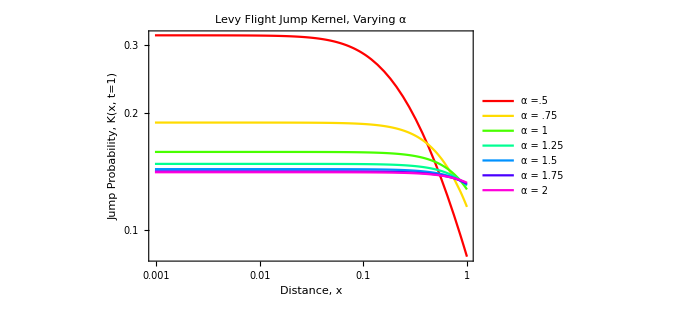

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],x],{α,{.5,.75,1,1.25,1.5, 1.75,2}}]//Evaluate,{x,0,1}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/7,1/7}] , LabelStyle->Directive[Bold, Black], PlotLabel -> Style["Levy Flight Jump Kernel, Varying α", FontSize -> 24], PlotLegends->{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 1.75","α = 2"}, Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Distance, x","Jump Probability, K(x, t=1)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]
```

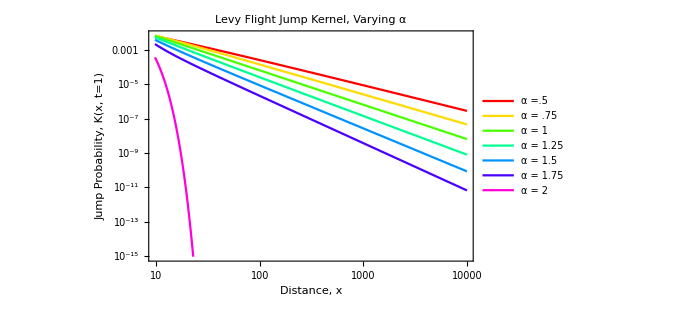

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],x],{α,{.5,.75,1,1.25,1.5, 1.75,2}}]//Evaluate,{x,0,10000}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/7,1/7}] , LabelStyle->Directive[Bold, Black], PlotLabel -> Style["Levy Flight Jump Kernel, Varying α", FontSize -> 24], PlotLegends->{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 1.75","α = 2"}, Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Distance, x","Jump Probability, K(x, t=1)",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]
```

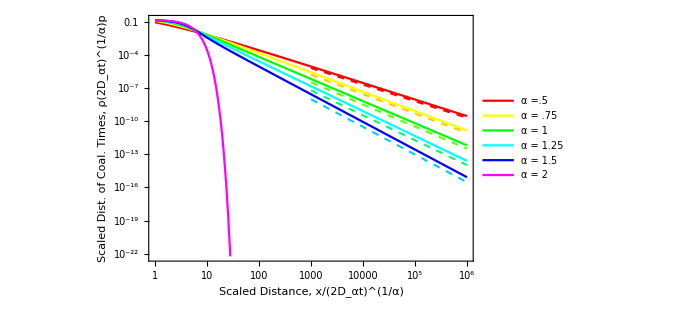

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],xdimensionless],{α,{.5,.75,1,1.25,1.5,2}}]//Evaluate,{xdimensionless,1,10^6}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/6,1/6}] , LabelStyle->Directive[ Black], PlotLabel -> Style["", FontSize -> 18], PlotLegends->Placed[{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 2"},{0.15,0.4}], Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],LogLogPlot[Table[Pi^-1*Sin[Pi*α/2]*Gamma[1 +α]*xdimensionless^(-α-1),{α,{.5,.75,1,1.25,1.5,2}}]//Evaluate,{xdimensionless,10^3,10^6} , LabelStyle->Directive[ Black], PlotStyle->Table[{Hue[h-.1,1,1],Dashed,Thickness[.003]},{h,.1,1.1-1/7.5,1/7.5}] ,PlotLabel -> Style["", FontSize -> 18],  Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Scaled Distance, x/(2D_αt)^(1/α)","Scaled Dist. of Coal. Times, ρ(2D_αt)^(1/α)p",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,PlotRangePadding->Scaled[.06],Axes->False]
```

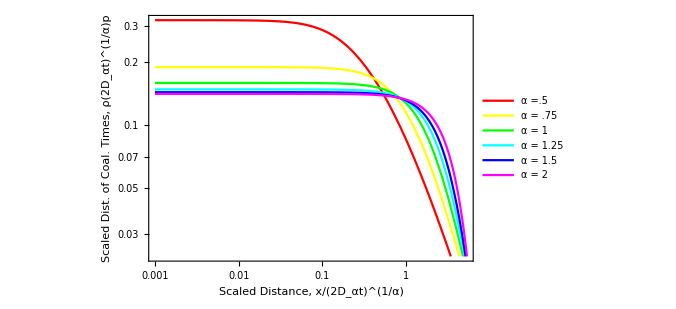

```mathematica
Show[LogLogPlot[Table[PDF[StableDistribution[0,α,0,0,2],xdimensionless],{α,{.5,.75,1,1.25,1.5,2}}]//Evaluate,{xdimensionless,.001,10}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/6,1/6}] , LabelStyle->Directive[ Black], PlotLabel -> Style["", FontSize -> 18], PlotLegends->Placed[{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 2"},{0.15,0.4}], Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Scaled Distance, x/(2D_αt)^(1/α)","Scaled Dist. of Coal. Times, ρ(2D_αt)^(1/α)p",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,PlotRangePadding->Scaled[.06],Axes->False]
```

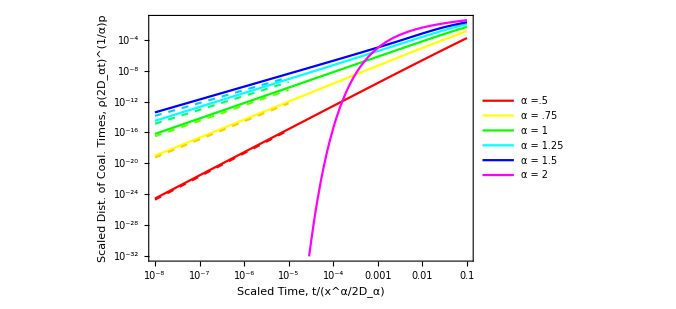

```mathematica
Show[LogLogPlot[Table[(timedimensionless)^(1/α)*PDF[StableDistribution[0,α,0,0,2],(timedimensionless)^(-1/(α +1))],{α,{.5,.75,1,1.25,1.5,2}}]//Evaluate,{timedimensionless,10^-8,10^-1}, PlotStyle->Table[Hue[h-.1,1,1],{h,.1,1.1-1/6,1/6}] , LabelStyle->Directive[ Black], PlotLabel -> Style["", FontSize -> 18], PlotLegends->Placed[{"α =.5","α = .75","α = 1","α =  1.25","α = 1.5","α = 2"},{0.9,0.4}], Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],LogLogPlot[Table[Pi^-1*Sin[Pi*α/2]*Gamma[1 +α]*timedimensionless^(1 + 1/α),{α,{.5,.75,1,1.25,1.5, 2}}]//Evaluate,{timedimensionless,10^-8,10^-5}, PlotStyle->Table[{Hue[h-.1,1,1],Dashed,Thickness[.003]},{h,.1,1.1-1/7.5,1/7.5}] , LabelStyle->Directive[ Black], PlotLabel -> Style["", FontSize -> 18],  Frame->True,FrameLabel->{"xlabel","ylabel"},FrameStyle->{{None,Black},{None,Black}}],goodlabel["Scaled Time, t/(x^α/2D_α)","Scaled Dist. of Coal. Times, ρ(2D_αt)^(1/α)p",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,PlotRangePadding->Scaled[.06],Axes->False]
```